```mathematica
Needs["ExperimentEvaluation`"]
```

## Experiments I

```mathematica
data=readAllFiles[{"20110803/GP4D_1000","GPAT4D_SSM_500"},labels,ReplaceParamValues->{"FC55"->"ZFC55"}];
```

```mathematica
StringReplace[#,"~/java/exp/"->""]&/@FileNames["~/java/exp/GPAT_MAZE_MAP*"]
```

{GPAT_MAZE_MAP2_NOVER,GPAT_MAZE_MAP2_ORIG,GPAT_MAZE_MAP2_RF4,GPAT_MAZE_MAP2_RF8,GPAT_MAZE_MAP3_NOVER,GPAT_MAZE_MAP3_ORIG,GPAT_MAZE_MAP3_RF4,GPAT_MAZE_MAP3_RF8,GPAT_MAZE_MAP4_NOVER,GPAT_MAZE_MAP4_ORIG,GPAT_MAZE_MAP4_RF4,GPAT_MAZE_MAP4_RF8}

```mathematica
data=readAllFiles[(StringReplace[#,"~/java/exp/"->""]&/@FileNames["~/java/exp/GP_MAZE_MAP*"])~Join~(StringReplace[#,"~/java/exp/"->""]&/@FileNames["~/java/exp/GPAT_MAZE_MAP*"])~Join~{"GPATGP_MAZE_ALL"},labels];
```

```mathematica
names=Flatten@Transpose@{{"GP_MAZE_MAP2_ORIG","GP_MAZE_MAP2_RF4","GP_MAZE_MAP2_RF8","GP_MAZE_MAP2_NOVER","GP_MAZE_MAP3_ORIG","GP_MAZE_MAP3_RF4","GP_MAZE_MAP3_RF8","GP_MAZE_MAP3_NOVER"},{"GPAT_MAZE_MAP2_ORIG","GPAT_MAZE_MAP2_RF4","GPAT_MAZE_MAP2_RF8","GPAT_MAZE_MAP2_NOVER","GPAT_MAZE_MAP3_ORIG","GPAT_MAZE_MAP3_RF4","GPAT_MAZE_MAP3_RF8","GPAT_MAZE_MAP3_NOVER"}};
```

```mathematica
labels={"GP_MAP2_NOVER","GP_MAP2_ORIG","GP_MAP2_RF4","GP_MAP2_RF8","GP_MAP3_NOVER","GP_MAP3_ORIG","GP_MAP3_RF4","GP_MAP3_RF8","GP_MAP4_NOVER","GP_MAP4_ORIG","GP_MAP4_RF4","GP_MAP4_RF8","GPAT_MAP2_NOVER","GPAT_MAP2_ORIG","GPAT_MAP2_RF4","GPAT_MAP2_RF8","GPAT_MAP3_NOVER","GPAT_MAP3_ORIG","GPAT_MAP3_RF4","GPAT_MAP3_RF8","GPAT_MAP4_NOVER","GPAT_MAP4_ORIG","GPAT_MAP4_RF4","GATP_MAP4_RF8","GPATGP_MAP2_ORIG","GPATGP_MAP2_NOVER","GPATGP_MAP2_RF4","GPATGP_MAP2_RF8","GPATGP_MAP3_ORIG","GPATGP_MAP3_NOVER","GPATGP_MAP3_RF4","GPATGP_MAP3_RF8","GPATGP_MAP24_ORIG","GPATGP_MAP4_NOVER","GPATGP_MAP4_RF4","GPATGP_MAP4_RF8"};
```

```mathematica
data=readAllFiles[names,labels];
```

```mathematica
listAllFiles[{"GP_4D_FC55_1000_old","GPAT_4D_FC55_ALL"}]
```

{{/Users/drchaj1/java/exp/GP_4D_FC55_1000_old/experiments_010.txt,/Users/drchaj1/java/exp/GP_4D_FC55_1000_old/parameters_010.txt},{/Users/drchaj1/java/exp/GPAT_4D_FC55_ALL/experiments_001.txt,/Users/drchaj1/java/exp/GPAT_4D_FC55_ALL/parameters_001.txt},{/Users/drchaj1/java/exp/GPAT_4D_FC55_ALL/experiments_002.txt,/Users/drchaj1/java/exp/GPAT_4D_FC55_ALL/parameters_002.txt},{/Users/drchaj1/java/exp/GPAT_4D_FC55_ALL/experiments_003.txt,/Users/drchaj1/java/exp/GPAT_4D_FC55_ALL/parameters_003.txt},{/Users/drchaj1/java/exp/GPAT_4D_FC55_ALL/experiments_004.txt,/Users/drchaj1/java/exp/GPAT_4D_FC55_ALL/parameters_004.txt},{/Users/drchaj1/java/exp/GPAT_4D_FC55_ALL/experiments_005.txt,/Users/drchaj1/java/exp/GPAT_4D_FC55_ALL/parameters_005.txt},{/Users/drchaj1/java/exp/GPAT_4D_FC55_ALL/experiments_006.txt,/Users/drchaj1/java/exp/GPAT_4D_FC55_ALL/parameters_006.txt}}

```mathematica
names={"GP_MAP2_200_old","GPAT_MAP2_ALL","GP_2D_H_1000_old","GPAT_2D_H_ALL","GP_4D_F_1000_old","GPAT_4D_F_ALL","GP_4D_FC55_1000_old","GPAT_4D_FC55_ALL"};
labels=Flatten[Outer[StringJoin[#2,#1]&,{"MAP2","2D_H","4D_F","4D_FC55"},{"GP_","GPAT_BASIC_","GPAT_RANDOM_","GPAT_CONSTANT1_","GPAT_SIMPLE_","GPAT_SIMPLE_REC_","GPAT_SIMPLE_REC2_","GPAT_SIMPLE_REC3_","GPAT_SIMPLE_ROOTO_","GPAT_SIMPLE_REC4_","GPAT_SIMPLE_SIMPLE2_","GPAT_SIMPLE_REC5_"}]];
data=readAllFiles[names,labels];
```

```mathematica
StringReplace[#,"~/java/exp/"->""]&/@FileNames["~/java/exp/GPAT_MAZE_MAP*"]
```

{GPAT_MAZE_MAP2_NOVER,GPAT_MAZE_MAP2_ORIG,GPAT_MAZE_MAP2_RF4,GPAT_MAZE_MAP2_RF8,GPAT_MAZE_MAP3_NOVER,GPAT_MAZE_MAP3_ORIG,GPAT_MAZE_MAP3_RF4,GPAT_MAZE_MAP3_RF8,GPAT_MAZE_MAP4_NOVER,GPAT_MAZE_MAP4_ORIG,GPAT_MAZE_MAP4_RF4,GPAT_MAZE_MAP4_RF8}

```mathematica
keepOnlyBest[StringReplace[#,"~/java/exp/"->""]&/@FileNames["~/java/exp/GPATGP_MAZE_ALL"],"BSF",60]
```

```mathematica
changingParameters[data]
```

{GPAT.FUNCTION_IMPL,GP.MAX_EVALUATIONS,GP.MUTATION_CAUCHY_PROBABILITY,GP.TYPE,SOLVER,SYMBOLIC_REGRESSION_4D.F}

```mathematica
sortedData = data;
```

```mathematica
sortedData=sortDataByParams[data,{"SYMBOLIC_REGRESSION_4D.F"},ReplaceParamValues->{"ZFC55"->"FC55"}];
```

```mathematica
data=readAllFiles[{"GPAT_4D_FC55_ALL","A"}];
```

```mathematica
saveData[data,"B"]
```

```mathematica
printAsTable[sortedData,{"SOLVER","MAZE.MAP","SYMBOLIC_REGRESSION_4D.F","GP.TARGET_FITNESS","GP.TYPE","GPAT.FUNCTION_IMPL","GPAT.MUTATION_HEAVY_PROB","GPAT.MUTATION_HEAVY_POWER","GPAT.SPECIES_SIZE_MEAN"}]
```

ID | PARAM FILE | SOLVER | MAZE.MAP | SYMBOLIC_REGRESSION_4D.F | GP.TARGET_FITNESS | GP.TYPE | GPAT.FUNCTION_IMPL | GPAT.MUTATION_HEAVY_PROB | GPAT.MUTATION_HEAVY_POWER | GPAT.SPECIES_SIZE_MEAN
GP_MAP2 | GP_MAP2_200_old/parameters_001.txt | GP | map2.csv | NONE | 50. | gp.GP | NONE | NONE | NONE | NONE
GPAT_BASIC_MAP2 | GPAT_MAP2_ALL/parameters_001.txt | GPAT | map2.csv | NONE | 40. | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_RANDOM_MAP2 | GPAT_MAP2_ALL/parameters_002.txt | GPAT | map2.csv | NONE | 40. | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_CONSTANT1_MAP2 | GPAT_MAP2_ALL/parameters_003.txt | GPAT | map2.csv | NONE | 40. | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_MAP2 | GPAT_MAP2_ALL/parameters_004.txt | GPAT | map2.csv | NONE | 40. | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_REC_MAP2 | GPAT_MAP2_ALL/parameters_005.txt | GPAT | map2.csv | NONE | 40. | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_REC2_MAP2 | GPAT_MAP2_ALL/parameters_006.txt | GPAT | map2.csv | NONE | 40. | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_REC3_MAP2 | GPAT_MAP2_ALL/parameters_007.txt | GPAT | map2.csv | NONE | 40. | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_ROOTO_MAP2 | GPAT_MAP2_ALL/parameters_008.txt | GPAT | map2.csv | NONE | 40. | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_REC4_MAP2 | GPAT_MAP2_ALL/parameters_009.txt | GPAT | map2.csv | NONE | 40. | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_SIMPLE2_MAP2 | GPAT_MAP2_ALL/parameters_010.txt | GPAT | map2.csv | NONE | 40. | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_REC5_MAP2 | GPAT_MAP2_ALL/parameters_011.txt | GPAT | map2.csv | NONE | 40. | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GP_2D_H | GP_2D_H_1000_old/parameters_008.txt | GP | NONE | NONE | 0.95 | gp.GP | NONE | NONE | NONE | NONE
GPAT_BASIC_2D_H | GPAT_2D_H_ALL/parameters_001.txt | GPAT | NONE | NONE | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_RANDOM_2D_H | GPAT_2D_H_ALL/parameters_002.txt | GPAT | NONE | NONE | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_CONSTANT1_2D_H | GPAT_2D_H_ALL/parameters_003.txt | GPAT | NONE | NONE | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_2D_H | GPAT_2D_H_ALL/parameters_004.txt | GPAT | NONE | NONE | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_REC_2D_H | GPAT_2D_H_ALL/parameters_005.txt | GPAT | NONE | NONE | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_REC2_2D_H | GPAT_2D_H_ALL/parameters_006.txt | GPAT | NONE | NONE | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_REC3_2D_H | GPAT_2D_H_ALL/parameters_007.txt | GPAT | NONE | NONE | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_ROOTO_2D_H | GPAT_2D_H_ALL/parameters_008.txt | GPAT | NONE | NONE | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_REC4_2D_H | GPAT_2D_H_ALL/parameters_009.txt | GPAT | NONE | NONE | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_SIMPLE2_2D_H | GPAT_2D_H_ALL/parameters_010.txt | GPAT | NONE | NONE | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_REC5_2D_H | GPAT_2D_H_ALL/parameters_011.txt | GPAT | NONE | NONE | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GP_4D_F | GP_4D_F_1000_old/parameters_006.txt | GP | NONE | F | 0.95 | gp.GP | NONE | NONE | NONE | NONE
GPAT_BASIC_4D_F | GPAT_4D_F_ALL/parameters_001.txt | GPAT | NONE | F | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_RANDOM_4D_F | GPAT_4D_F_ALL/parameters_002.txt | GPAT | NONE | F | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_CONSTANT1_4D_F | GPAT_4D_F_ALL/parameters_003.txt | GPAT | NONE | F | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_4D_F | GPAT_4D_F_ALL/parameters_004.txt | GPAT | NONE | F | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_REC_4D_F | GPAT_4D_F_ALL/parameters_005.txt | GPAT | NONE | F | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_REC2_4D_F | GPAT_4D_F_ALL/parameters_006.txt | GPAT | NONE | F | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_REC3_4D_F | GPAT_4D_F_ALL/parameters_007.txt | GPAT | NONE | F | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_ROOTO_4D_F | GPAT_4D_F_ALL/parameters_008.txt | GPAT | NONE | F | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_REC4_4D_F | GPAT_4D_F_ALL/parameters_009.txt | GPAT | NONE | F | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_SIMPLE2_4D_F | GPAT_4D_F_ALL/parameters_010.txt | GPAT | NONE | F | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_REC5_4D_F | GPAT_4D_F_ALL/parameters_011.txt | GPAT | NONE | F | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GP_4D_FC55 | GP_4D_FC55_1000_old/parameters_010.txt | GP | NONE | FC55 | 0.95 | gp.GP | NONE | NONE | NONE | NONE
GPAT_BASIC_4D_FC55 | GPAT_4D_FC55_ALL/parameters_001.txt | GPAT | NONE | FC55 | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_RANDOM_4D_FC55 | GPAT_4D_FC55_ALL/parameters_002.txt | GPAT | NONE | FC55 | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_CONSTANT1_4D_FC55 | GPAT_4D_FC55_ALL/parameters_003.txt | GPAT | NONE | FC55 | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_4D_FC55 | GPAT_4D_FC55_ALL/parameters_004.txt | GPAT | NONE | FC55 | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_REC_4D_FC55 | GPAT_4D_FC55_ALL/parameters_005.txt | GPAT | NONE | FC55 | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_REC2_4D_FC55 | GPAT_4D_FC55_ALL/parameters_006.txt | GPAT | NONE | FC55 | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_REC3_4D_FC55 | GPAT_4D_FC55_ALL/parameters_007.txt | GPAT | NONE | FC55 | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_ROOTO_4D_FC55 | GPAT_4D_FC55_ALL/parameters_008.txt | GPAT | NONE | FC55 | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_REC4_4D_FC55 | GPAT_4D_FC55_ALL/parameters_009.txt | GPAT | NONE | FC55 | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_SIMPLE2_4D_FC55 | GPAT_4D_FC55_ALL/parameters_010.txt | GPAT | NONE | FC55 | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_REC5_4D_FC55 | GPAT_4D_FC55_ALL/parameters_011.txt | GPAT | NONE | FC55 | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.

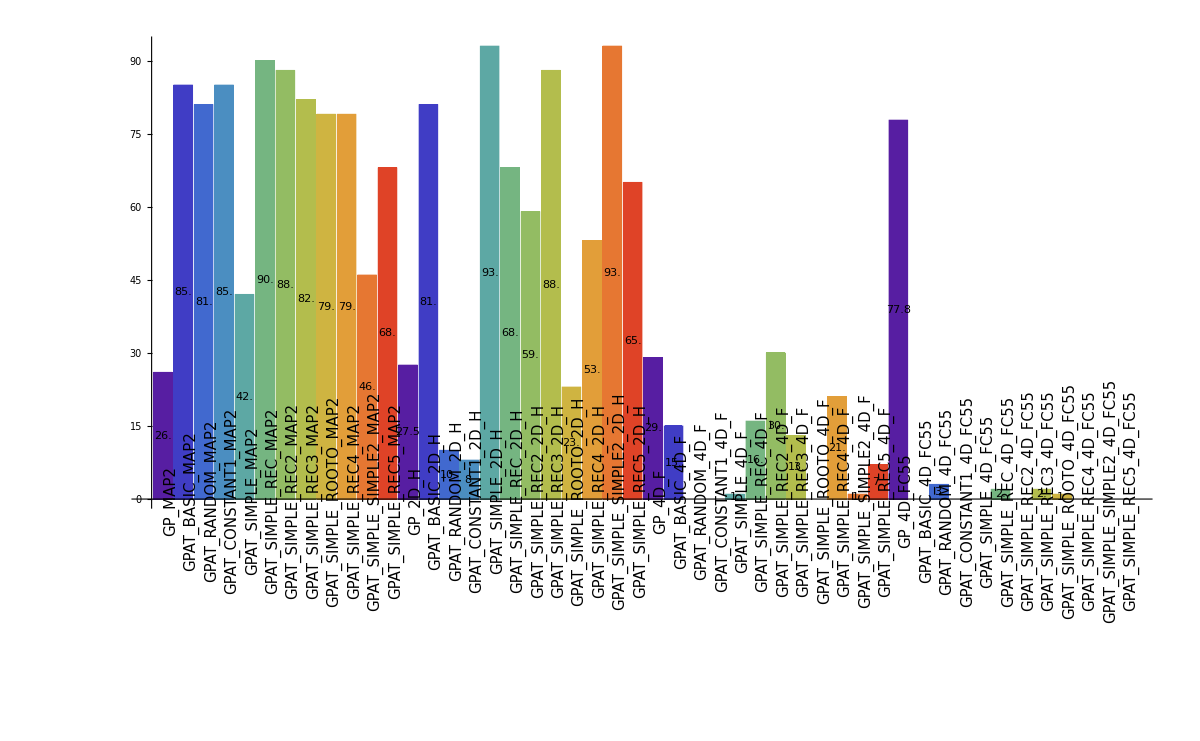

```mathematica
plotBooleanAsBarChart[sortedData,"SUCCESS",12]
```

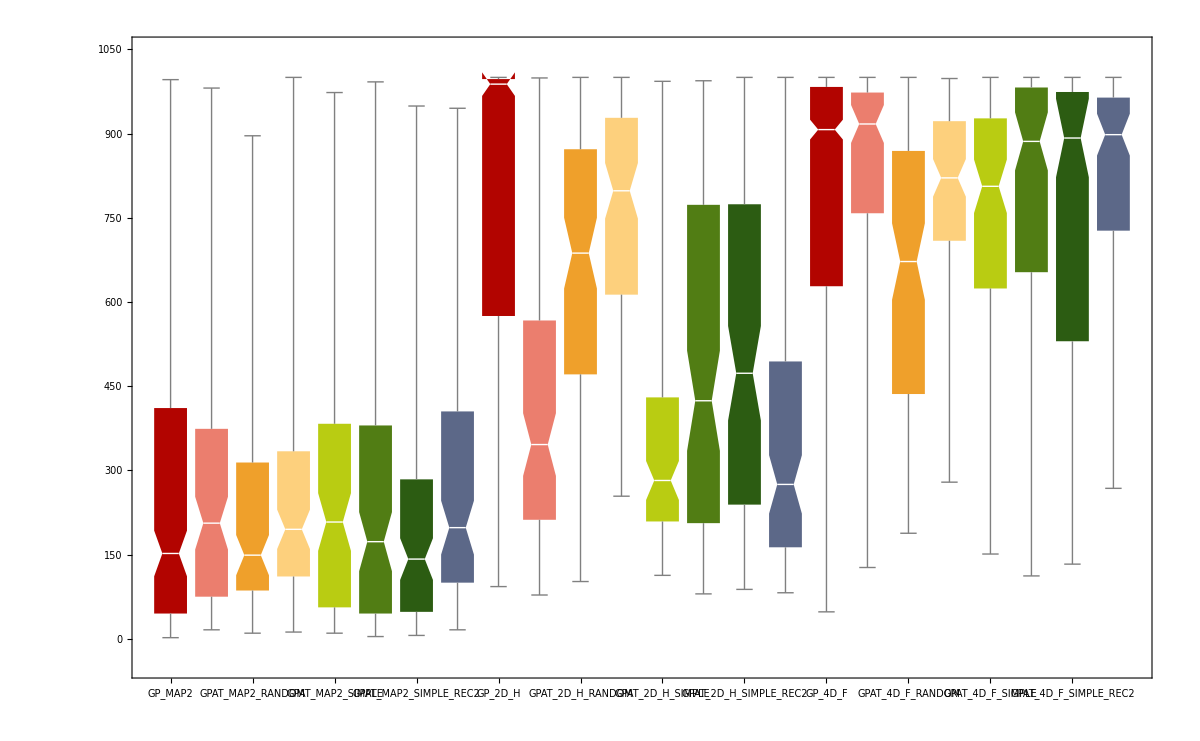

```mathematica
plotAsBoxWhiskerChart[sortedData,"BSFG",8]
```

## Experiments II

```mathematica
names={"GPAT_maze-1_REC7PAR","GPAT_maze-2_REC7PAR"};
data=readAllFiles[names,Null,ReplaceParamValues->{"FC55"->"ZFC55"}];
data=assignLabelsByParameters[data,{"SOLVER","ID","SYMBOLIC_REGRESSION.F","MAZE.MAP","PROBLEM","GPAT.DISTANCE","GPAT.DISTANCE_REC5_C1","GPAT.DISTANCE_REC5_C2"},{"ZFC55"->"FC55",RegularExpression["gp.demo.SymbolicRegression.*"]->"","gp.demo.MazeRangeFinders"->"RF4","gp.demo.Maze"->"ORIG","map"->"MAP",".csv"->""}];
changingParameters[data]
```

{GPAT.DISTANCE_REC5_C1,GPAT.DISTANCE_REC5_C2,MAZE.MAP,PROBLEM}

```mathematica
(*sdata=selectData[data,{"SOLVER"->"GPAT","GPAT.DISTANCE"->{"SIMPLE_REC5","SIMPLE_REC6","SIMPLE_REC7"}}];*)
(*sdata=removeData[data,{"GPAT.DISTANCE"->{"CONSTANT","ROOTO","SIMPLE","SIMPLE_REC","SIMPLE_REC2","SIMPLE_REC3"}}];*)
sdata=removeData[data,{"GPAT.DISTANCE"->{"SIMPLE2","SIMPLE_REC4","SIMPLE_REC5","SIMPLE_REC6"}}];
sortedData = sortDataByParams[sdata,{"ID","SYMBOLIC_REGRESSION.F","MAZE.MAP","SOLVER","GPAT.DISTANCE","PROBLEM"}];
printAsTable[sortedData,{"SOLVER","GPAT.FUNCTION_IMPL","ID","SYMBOLIC_REGRESSION.F","MAZE.MAP","GPAT.DISTANCE","GP.TARGET_FITNESS","PROBLEM"}]
```

ID | PARAM FILE | SOLVER | GPAT.FUNCTION_IMPL | ID | SYMBOLIC_REGRESSION.F | MAZE.MAP | GPAT.DISTANCE | GP.TARGET_FITNESS | PROBLEM
GPAT_MAZE_MAP2_ORIG_SIMPLE_REC7_0.1_0.1 | GPAT_maze-1_REC7PAR/parameters_001.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map2.csv | SIMPLE_REC7 | 40. | gp.demo.Maze
GPAT_MAZE_MAP2_ORIG_SIMPLE_REC7_0.1_0.5 | GPAT_maze-1_REC7PAR/parameters_002.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map2.csv | SIMPLE_REC7 | 40. | gp.demo.Maze
GPAT_MAZE_MAP2_ORIG_SIMPLE_REC7_0.1_0.8 | GPAT_maze-1_REC7PAR/parameters_003.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map2.csv | SIMPLE_REC7 | 40. | gp.demo.Maze
GPAT_MAZE_MAP2_ORIG_SIMPLE_REC7_0.1_0.9 | GPAT_maze-1_REC7PAR/parameters_004.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map2.csv | SIMPLE_REC7 | 40. | gp.demo.Maze
GPAT_MAZE_MAP2_ORIG_SIMPLE_REC7_0.1_0.95 | GPAT_maze-1_REC7PAR/parameters_005.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map2.csv | SIMPLE_REC7 | 40. | gp.demo.Maze
GPAT_MAZE_MAP2_ORIG_SIMPLE_REC7_0.5_0.1 | GPAT_maze-1_REC7PAR/parameters_006.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map2.csv | SIMPLE_REC7 | 40. | gp.demo.Maze
GPAT_MAZE_MAP2_ORIG_SIMPLE_REC7_0.5_0.5 | GPAT_maze-1_REC7PAR/parameters_007.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map2.csv | SIMPLE_REC7 | 40. | gp.demo.Maze
GPAT_MAZE_MAP2_ORIG_SIMPLE_REC7_0.5_0.8 | GPAT_maze-1_REC7PAR/parameters_008.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map2.csv | SIMPLE_REC7 | 40. | gp.demo.Maze
GPAT_MAZE_MAP2_ORIG_SIMPLE_REC7_0.5_0.9 | GPAT_maze-1_REC7PAR/parameters_009.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map2.csv | SIMPLE_REC7 | 40. | gp.demo.Maze
GPAT_MAZE_MAP2_ORIG_SIMPLE_REC7_0.5_0.95 | GPAT_maze-1_REC7PAR/parameters_010.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map2.csv | SIMPLE_REC7 | 40. | gp.demo.Maze
GPAT_MAZE_MAP2_ORIG_SIMPLE_REC7_0.9_0.1 | GPAT_maze-1_REC7PAR/parameters_011.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map2.csv | SIMPLE_REC7 | 40. | gp.demo.Maze
GPAT_MAZE_MAP2_ORIG_SIMPLE_REC7_0.9_0.5 | GPAT_maze-1_REC7PAR/parameters_012.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map2.csv | SIMPLE_REC7 | 40. | gp.demo.Maze
GPAT_MAZE_MAP2_ORIG_SIMPLE_REC7_0.9_0.8 | GPAT_maze-1_REC7PAR/parameters_013.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map2.csv | SIMPLE_REC7 | 40. | gp.demo.Maze
GPAT_MAZE_MAP2_ORIG_SIMPLE_REC7_0.9_0.9 | GPAT_maze-1_REC7PAR/parameters_014.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map2.csv | SIMPLE_REC7 | 40. | gp.demo.Maze
GPAT_MAZE_MAP2_ORIG_SIMPLE_REC7_0.9_0.95 | GPAT_maze-1_REC7PAR/parameters_015.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map2.csv | SIMPLE_REC7 | 40. | gp.demo.Maze
GPAT_MAZE_MAP4_RF4_SIMPLE_REC7_0.1_0.1 | GPAT_maze-2_REC7PAR/parameters_001.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map4.csv | SIMPLE_REC7 | 40. | gp.demo.MazeRangeFinders
GPAT_MAZE_MAP4_RF4_SIMPLE_REC7_0.1_0.5 | GPAT_maze-2_REC7PAR/parameters_002.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map4.csv | SIMPLE_REC7 | 40. | gp.demo.MazeRangeFinders
GPAT_MAZE_MAP4_RF4_SIMPLE_REC7_0.1_0.8 | GPAT_maze-2_REC7PAR/parameters_003.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map4.csv | SIMPLE_REC7 | 40. | gp.demo.MazeRangeFinders
GPAT_MAZE_MAP4_RF4_SIMPLE_REC7_0.1_0.9 | GPAT_maze-2_REC7PAR/parameters_004.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map4.csv | SIMPLE_REC7 | 40. | gp.demo.MazeRangeFinders
GPAT_MAZE_MAP4_RF4_SIMPLE_REC7_0.1_0.95 | GPAT_maze-2_REC7PAR/parameters_005.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map4.csv | SIMPLE_REC7 | 40. | gp.demo.MazeRangeFinders
GPAT_MAZE_MAP4_RF4_SIMPLE_REC7_0.5_0.1 | GPAT_maze-2_REC7PAR/parameters_006.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map4.csv | SIMPLE_REC7 | 40. | gp.demo.MazeRangeFinders
GPAT_MAZE_MAP4_RF4_SIMPLE_REC7_0.5_0.5 | GPAT_maze-2_REC7PAR/parameters_007.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map4.csv | SIMPLE_REC7 | 40. | gp.demo.MazeRangeFinders
GPAT_MAZE_MAP4_RF4_SIMPLE_REC7_0.5_0.8 | GPAT_maze-2_REC7PAR/parameters_008.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map4.csv | SIMPLE_REC7 | 40. | gp.demo.MazeRangeFinders
GPAT_MAZE_MAP4_RF4_SIMPLE_REC7_0.5_0.9 | GPAT_maze-2_REC7PAR/parameters_009.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map4.csv | SIMPLE_REC7 | 40. | gp.demo.MazeRangeFinders
GPAT_MAZE_MAP4_RF4_SIMPLE_REC7_0.5_0.95 | GPAT_maze-2_REC7PAR/parameters_010.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map4.csv | SIMPLE_REC7 | 40. | gp.demo.MazeRangeFinders
GPAT_MAZE_MAP4_RF4_SIMPLE_REC7_0.9_0.1 | GPAT_maze-2_REC7PAR/parameters_011.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map4.csv | SIMPLE_REC7 | 40. | gp.demo.MazeRangeFinders
GPAT_MAZE_MAP4_RF4_SIMPLE_REC7_0.9_0.5 | GPAT_maze-2_REC7PAR/parameters_012.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map4.csv | SIMPLE_REC7 | 40. | gp.demo.MazeRangeFinders
GPAT_MAZE_MAP4_RF4_SIMPLE_REC7_0.9_0.8 | GPAT_maze-2_REC7PAR/parameters_013.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map4.csv | SIMPLE_REC7 | 40. | gp.demo.MazeRangeFinders
GPAT_MAZE_MAP4_RF4_SIMPLE_REC7_0.9_0.9 | GPAT_maze-2_REC7PAR/parameters_014.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map4.csv | SIMPLE_REC7 | 40. | gp.demo.MazeRangeFinders
GPAT_MAZE_MAP4_RF4_SIMPLE_REC7_0.9_0.95 | GPAT_maze-2_REC7PAR/parameters_015.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map4.csv | SIMPLE_REC7 | 40. | gp.demo.MazeRangeFinders

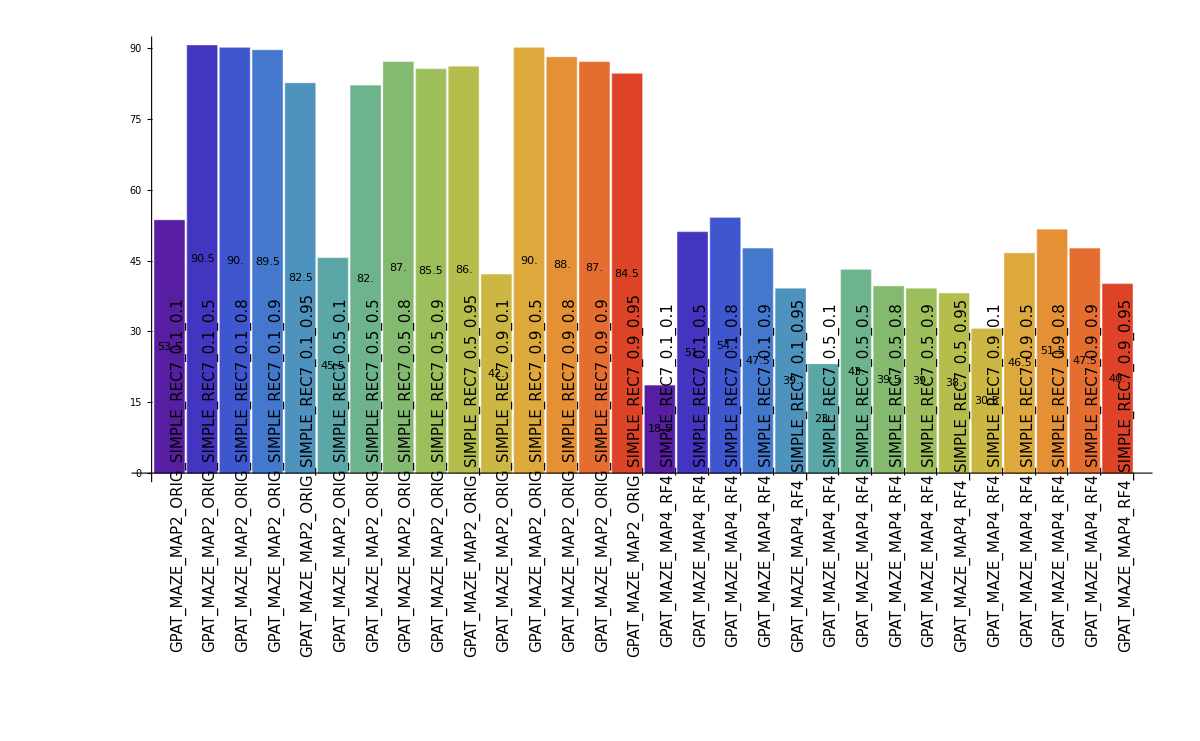

```mathematica
plotBooleanAsBarChart[sortedData,"SUCCESS",15]
```

## Experiments III

```mathematica
(*names={"GP_RANDOMPAR","GP_BASICPAR","GP_RESTO2PAR","GP_TREEPPAR","GP_TREEP2PAR"};*)
(*names={"NEAT_BASIC","NEAT_DELTAS","GP","GP_RANDOM","GP_BASIC","GP_RESTO2","GP_TREEP","GP_TREEP2"};*)
names={"NEAT_DELTAS"};
(*names={"GP_TREEPPAR"};*)
(*names={"GP_1D*","GPAT_1D*","GP_2D*","GPAT_2D*"};*)
(*names={"GP_1D*","GPAT_1D*"};*)
(*names={"GP_2D*","GPAT_2D*"};*)
(*names={"GP_3D*","GPAT_3D*"};*)
(*names={"GP_4D*","GPAT_4D*"};*)
(*names={"GP_maze*","GPAT_maze*"};*)
(*names={"GP_1D*","GPAT_1D*","GP_2D*","GPAT_2D*","GP_3D*","GPAT_3D*","GP_4D*","GPAT_4D*","GP_maze*","GPAT_maze*"};*)
(*names={"GP_maze-1_BASIC","GP_maze-2_BASIC"};*)
data=readAllFiles[names,Null,ReplaceParamValues->{"FC55"->"ZFC55"}];
data=assignLabelsByParameters[data,{"SOLVER","ID","SYMBOLIC_REGRESSION.F","MAZE.MAP","PROBLEM","GPAT.DISTANCE","GP.DISTANCE","GPEFS.SPECIES_REPRODUCTION_RATIO","GPEFS.SPECIES_SIZE_MEAN","NEAT.distanceDelta"},{"ZFC55"->"FC55",RegularExpression["gp.demo.SymbolicRegression.*"]->"","gp.demo.MazeRangeFinders"->"RF4","gp.demo.Maze"->"ORIG","map"->"MAP",".csv"->""}];
changingParameters[data]
```

{GPAT.DISTANCE_PHENO_HIGH,GPAT.DISTANCE_PHENO_LOW,GPAT.DISTANCE_PHENO_STEPS,GP.TARGET_FITNESS,ID,MAZE.MAP,NEAT.distanceDelta,PROBLEM,SYMBOLIC_REGRESSION.F}

```mathematica
saveData[sortedData,"GP_TREEP"]
```

```mathematica
(*sdata=selectData[data,{"SOLVER"->"GPAT","GPAT.DISTANCE"->{"SIMPLE_REC5","SIMPLE_REC6","SIMPLE_REC7"}}];*)
(*sdata=removeData[data,{"GPAT.DISTANCE"->{"CONSTANT","ROOTO","SIMPLE","SIMPLE_REC","SIMPLE_REC2","SIMPLE_REC3"}}];*)
(*sdata=removeData[data,{"GPAT.DISTANCE"->{"SIMPLE2","SIMPLE_REC4","SIMPLE_REC5","SIMPLE_REC6"}}];*)
sdata=selectData[data,{"ID"->{"1D","2D","3D","4D"}}];
sdata=selectData[data,{"GPEFS.SPECIES_REPRODUCTION_RATIO"->{0.4},"GPEFS.SPECIES_SIZE_MEAN"->{5.}}];
sortedData = sortDataByParams[data,{"ID","SYMBOLIC_REGRESSION.F","MAZE.MAP","SOLVER","GPAT.DISTANCE","PROBLEM"}];
printAsTable[sortedData,{"SOLVER","GPAT.FUNCTION_IMPL","ID","SYMBOLIC_REGRESSION.F","MAZE.MAP","GPAT.DISTANCE","GP.DISTANCE","GPEFS.SPECIES_REPRODUCTION_RATIO","GPEFS.SPECIES_SIZE_MEAN","PROBLEM"}]
```

ID | PARAM FILE | SOLVER | GPAT.FUNCTION_IMPL | ID | SYMBOLIC_REGRESSION.F | MAZE.MAP | GPAT.DISTANCE | GP.DISTANCE | GPEFS.SPECIES_REPRODUCTION_RATIO | GPEFS.SPECIES_SIZE_MEAN | PROBLEM
NEAT_1D_F_0.5 | NEAT_DELTAS/parameters_001.txt | NEAT | NONE | 1D | F | NONE | NONE | NONE | NONE | NONE | gp.demo.SymbolicRegression
NEAT_1D_F_1. | NEAT_DELTAS/parameters_003.txt | NEAT | NONE | 1D | F | NONE | NONE | NONE | NONE | NONE | gp.demo.SymbolicRegression
NEAT_1D_F_2. | NEAT_DELTAS/parameters_005.txt | NEAT | NONE | 1D | F | NONE | NONE | NONE | NONE | NONE | gp.demo.SymbolicRegression
NEAT_1D_F_3. | NEAT_DELTAS/parameters_043.txt | NEAT | NONE | 1D | F | NONE | NONE | NONE | NONE | NONE | gp.demo.SymbolicRegression
NEAT_1D_F_5. | NEAT_DELTAS/parameters_057.txt | NEAT | NONE | 1D | F | NONE | NONE | NONE | NONE | NONE | gp.demo.SymbolicRegression
NEAT_1D_F_10. | NEAT_DELTAS/parameters_059.txt | NEAT | NONE | 1D | F | NONE | NONE | NONE | NONE | NONE | gp.demo.SymbolicRegression
NEAT_1D_F_15. | NEAT_DELTAS/parameters_061.txt | NEAT | NONE | 1D | F | NONE | NONE | NONE | NONE | NONE | gp.demo.SymbolicRegression
NEAT_1D_H_0.5 | NEAT_DELTAS/parameters_002.txt | NEAT | NONE | 1D | H | NONE | NONE | NONE | NONE | NONE | gp.demo.SymbolicRegression
NEAT_1D_H_1. | NEAT_DELTAS/parameters_004.txt | NEAT | NONE | 1D | H | NONE | NONE | NONE | NONE | NONE | gp.demo.SymbolicRegression
NEAT_1D_H_2. | NEAT_DELTAS/parameters_006.txt | NEAT | NONE | 1D | H | NONE | NONE | NONE | NONE | NONE | gp.demo.SymbolicRegression
NEAT_1D_H_3. | NEAT_DELTAS/parameters_044.txt | NEAT | NONE | 1D | H | NONE | NONE | NONE | NONE | NONE | gp.demo.SymbolicRegression
NEAT_1D_H_5. | NEAT_DELTAS/parameters_058.txt | NEAT | NONE | 1D | H | NONE | NONE | NONE | NONE | NONE | gp.demo.SymbolicRegression
NEAT_1D_H_10. | NEAT_DELTAS/parameters_060.txt | NEAT | NONE | 1D | H | NONE | NONE | NONE | NONE | NONE | gp.demo.SymbolicRegression
NEAT_1D_H_15. | NEAT_DELTAS/parameters_062.txt | NEAT | NONE | 1D | H | NONE | NONE | NONE | NONE | NONE | gp.demo.SymbolicRegression
NEAT_2D_I_0.5 | NEAT_DELTAS/parameters_007.txt | NEAT | NONE | 2D | I | NONE | NONE | NONE | NONE | NONE | gp.demo.SymbolicRegression2D
NEAT_2D_I_1. | NEAT_DELTAS/parameters_010.txt | NEAT | NONE | 2D | I | NONE | NONE | NONE | NONE | NONE | gp.demo.SymbolicRegression2D
NEAT_2D_I_2. | NEAT_DELTAS/parameters_013.txt | NEAT | NONE | 2D | I | NONE | NONE | NONE | NONE | NONE | gp.demo.SymbolicRegression2D
NEAT_2D_I_3. | NEAT_DELTAS/parameters_045.txt | NEAT | NONE | 2D | I | NONE | NONE | NONE | NONE | NONE | gp.demo.SymbolicRegression2D
NEAT_2D_I_5. | NEAT_DELTAS/parameters_063.txt | NEAT | NONE | 2D | I | NONE | NONE | NONE | NONE | NONE | gp.demo.SymbolicRegression2D
NEAT_2D_I_10. | NEAT_DELTAS/parameters_066.txt | NEAT | NONE | 2D | I | NONE | NONE | NONE | NONE | NONE | gp.demo.SymbolicRegression2D
NEAT_2D_I_15. | NEAT_DELTAS/parameters_069.txt | NEAT | NONE | 2D | I | NONE | NONE | NONE | NONE | NONE | gp.demo.SymbolicRegression2D
NEAT_2D_J_0.5 | NEAT_DELTAS/parameters_008.txt | NEAT | NONE | 2D | J | NONE | NONE | NONE | NONE | NONE | gp.demo.SymbolicRegression2D
NEAT_2D_J_1. | NEAT_DELTAS/parameters_011.txt | NEAT | NONE | 2D | J | NONE | NONE | NONE | NONE | NONE | gp.demo.SymbolicRegression2D
NEAT_2D_J_2. | NEAT_DELTAS/parameters_014.txt | NEAT | NONE | 2D | J | NONE | NONE | NONE | NONE | NONE | gp.demo.SymbolicRegression2D
NEAT_2D_J_3. | NEAT_DELTAS/parameters_046.txt | NEAT | NONE | 2D | J | NONE | NONE | NONE | NONE | NONE | gp.demo.SymbolicRegression2D
NEAT_2D_J_5. | NEAT_DELTAS/parameters_064.txt | NEAT | NONE | 2D | J | NONE | NONE | NONE | NONE | NONE | gp.demo.SymbolicRegression2D
NEAT_2D_J_10. | NEAT_DELTAS/parameters_067.txt | NEAT | NONE | 2D | J | NONE | NONE | NONE | NONE | NONE | gp.demo.SymbolicRegression2D
NEAT_2D_J_15. | NEAT_DELTAS/parameters_070.txt | NEAT | NONE | 2D | J | NONE | NONE | NONE | NONE | NONE | gp.demo.SymbolicRegression2D
NEAT_2D_K_0.5 | NEAT_DELTAS/parameters_009.txt | NEAT | NONE | 2D | K | NONE | NONE | NONE | NONE | NONE | gp.demo.SymbolicRegression2D
NEAT_2D_K_1. | NEAT_DELTAS/parameters_012.txt | NEAT | NONE | 2D | K | NONE | NONE | NONE | NONE | NONE | gp.demo.SymbolicRegression2D
NEAT_2D_K_2. | NEAT_DELTAS/parameters_015.txt | NEAT | NONE | 2D | K | NONE | NONE | NONE | NONE | NONE | gp.demo.SymbolicRegression2D
NEAT_2D_K_3. | NEAT_DELTAS/parameters_047.txt | NEAT | NONE | 2D | K | NONE | NONE | NONE | NONE | NONE | gp.demo.SymbolicRegression2D
NEAT_2D_K_5. | NEAT_DELTAS/parameters_065.txt | NEAT | NONE | 2D | K | NONE | NONE | NONE | NONE | NONE | gp.demo.SymbolicRegression2D
NEAT_2D_K_10. | NEAT_DELTAS/parameters_068.txt | NEAT | NONE | 2D | K | NONE | NONE | NONE | NONE | NONE | gp.demo.SymbolicRegression2D
NEAT_2D_K_15. | NEAT_DELTAS/parameters_071.txt | NEAT | NONE | 2D | K | NONE | NONE | NONE | NONE | NONE | gp.demo.SymbolicRegression2D
NEAT_3D_E_0.5 | NEAT_DELTAS/parameters_016.txt | NEAT | NONE | 3D | E | NONE | NONE | NONE | NONE | NONE | gp.demo.SymbolicRegression3D
NEAT_3D_E_1. | NEAT_DELTAS/parameters_019.txt | NEAT | NONE | 3D | E | NONE | NONE | NONE | NONE | NONE | gp.demo.SymbolicRegression3D
NEAT_3D_E_2. | NEAT_DELTAS/parameters_022.txt | NEAT | NONE | 3D | E | NONE | NONE | NONE | NONE | NONE | gp.demo.SymbolicRegression3D
NEAT_3D_E_3. | NEAT_DELTAS/parameters_048.txt | NEAT | NONE | 3D | E | NONE | NONE | NONE | NONE | NONE | gp.demo.SymbolicRegression3D
NEAT_3D_E_5. | NEAT_DELTAS/parameters_072.txt | NEAT | NONE | 3D | E | NONE | NONE | NONE | NONE | NONE | gp.demo.SymbolicRegression3D
NEAT_3D_E_10. | NEAT_DELTAS/parameters_075.txt | NEAT | NONE | 3D | E | NONE | NONE | NONE | NONE | NONE | gp.demo.SymbolicRegression3D
NEAT_3D_E_15. | NEAT_DELTAS/parameters_078.txt | NEAT | NONE | 3D | E | NONE | NONE | NONE | NONE | NONE | gp.demo.SymbolicRegression3D
NEAT_3D_H_0.5 | NEAT_DELTAS/parameters_017.txt | NEAT | NONE | 3D | H | NONE | NONE | NONE | NONE | NONE | gp.demo.SymbolicRegression3D
NEAT_3D_H_1. | NEAT_DELTAS/parameters_020.txt | NEAT | NONE | 3D | H | NONE | NONE | NONE | NONE | NONE | gp.demo.SymbolicRegression3D
NEAT_3D_H_2. | NEAT_DELTAS/parameters_023.txt | NEAT | NONE | 3D | H | NONE | NONE | NONE | NONE | NONE | gp.demo.SymbolicRegression3D
NEAT_3D_H_3. | NEAT_DELTAS/parameters_049.txt | NEAT | NONE | 3D | H | NONE | NONE | NONE | NONE | NONE | gp.demo.SymbolicRegression3D
NEAT_3D_H_5. | NEAT_DELTAS/parameters_073.txt | NEAT | NONE | 3D | H | NONE | NONE | NONE | NONE | NONE | gp.demo.SymbolicRegression3D
NEAT_3D_H_10. | NEAT_DELTAS/parameters_076.txt | NEAT | NONE | 3D | H | NONE | NONE | NONE | NONE | NONE | gp.demo.SymbolicRegression3D
NEAT_3D_H_15. | NEAT_DELTAS/parameters_079.txt | NEAT | NONE | 3D | H | NONE | NONE | NONE | NONE | NONE | gp.demo.SymbolicRegression3D
NEAT_3D_K_0.5 | NEAT_DELTAS/parameters_018.txt | NEAT | NONE | 3D | K | NONE | NONE | NONE | NONE | NONE | gp.demo.SymbolicRegression3D
NEAT_3D_K_1. | NEAT_DELTAS/parameters_021.txt | NEAT | NONE | 3D | K | NONE | NONE | NONE | NONE | NONE | gp.demo.SymbolicRegression3D
NEAT_3D_K_2. | NEAT_DELTAS/parameters_024.txt | NEAT | NONE | 3D | K | NONE | NONE | NONE | NONE | NONE | gp.demo.SymbolicRegression3D
NEAT_3D_K_3. | NEAT_DELTAS/parameters_050.txt | NEAT | NONE | 3D | K | NONE | NONE | NONE | NONE | NONE | gp.demo.SymbolicRegression3D
NEAT_3D_K_5. | NEAT_DELTAS/parameters_074.txt | NEAT | NONE | 3D | K | NONE | NONE | NONE | NONE | NONE | gp.demo.SymbolicRegression3D
NEAT_3D_K_10. | NEAT_DELTAS/parameters_077.txt | NEAT | NONE | 3D | K | NONE | NONE | NONE | NONE | NONE | gp.demo.SymbolicRegression3D
NEAT_3D_K_15. | NEAT_DELTAS/parameters_080.txt | NEAT | NONE | 3D | K | NONE | NONE | NONE | NONE | NONE | gp.demo.SymbolicRegression3D
NEAT_4D_C_0.5 | NEAT_DELTAS/parameters_025.txt | NEAT | NONE | 4D | C | NONE | NONE | NONE | NONE | NONE | gp.demo.SymbolicRegression4D
NEAT_4D_C_1. | NEAT_DELTAS/parameters_027.txt | NEAT | NONE | 4D | C | NONE | NONE | NONE | NONE | NONE | gp.demo.SymbolicRegression4D
NEAT_4D_C_2. | NEAT_DELTAS/parameters_029.txt | NEAT | NONE | 4D | C | NONE | NONE | NONE | NONE | NONE | gp.demo.SymbolicRegression4D
NEAT_4D_C_3. | NEAT_DELTAS/parameters_051.txt | NEAT | NONE | 4D | C | NONE | NONE | NONE | NONE | NONE | gp.demo.SymbolicRegression4D
NEAT_4D_C_5. | NEAT_DELTAS/parameters_081.txt | NEAT | NONE | 4D | C | NONE | NONE | NONE | NONE | NONE | gp.demo.SymbolicRegression4D
NEAT_4D_C_10. | NEAT_DELTAS/parameters_083.txt | NEAT | NONE | 4D | C | NONE | NONE | NONE | NONE | NONE | gp.demo.SymbolicRegression4D
NEAT_4D_C_15. | NEAT_DELTAS/parameters_085.txt | NEAT | NONE | 4D | C | NONE | NONE | NONE | NONE | NONE | gp.demo.SymbolicRegression4D
NEAT_4D_F_0.5 | NEAT_DELTAS/parameters_026.txt | NEAT | NONE | 4D | F | NONE | NONE | NONE | NONE | NONE | gp.demo.SymbolicRegression4D
NEAT_4D_F_1. | NEAT_DELTAS/parameters_028.txt | NEAT | NONE | 4D | F | NONE | NONE | NONE | NONE | NONE | gp.demo.SymbolicRegression4D
NEAT_4D_F_2. | NEAT_DELTAS/parameters_030.txt | NEAT | NONE | 4D | F | NONE | NONE | NONE | NONE | NONE | gp.demo.SymbolicRegression4D
NEAT_4D_F_3. | NEAT_DELTAS/parameters_052.txt | NEAT | NONE | 4D | F | NONE | NONE | NONE | NONE | NONE | gp.demo.SymbolicRegression4D
NEAT_4D_F_5. | NEAT_DELTAS/parameters_082.txt | NEAT | NONE | 4D | F | NONE | NONE | NONE | NONE | NONE | gp.demo.SymbolicRegression4D
NEAT_4D_F_10. | NEAT_DELTAS/parameters_084.txt | NEAT | NONE | 4D | F | NONE | NONE | NONE | NONE | NONE | gp.demo.SymbolicRegression4D
NEAT_4D_F_15. | NEAT_DELTAS/parameters_086.txt | NEAT | NONE | 4D | F | NONE | NONE | NONE | NONE | NONE | gp.demo.SymbolicRegression4D
NEAT_4D_G_0.5 | NEAT_DELTAS/parameters_031.txt | NEAT | NONE | 4D | G | NONE | NONE | NONE | NONE | NONE | gp.demo.SymbolicRegression4D
NEAT_4D_G_1. | NEAT_DELTAS/parameters_033.txt | NEAT | NONE | 4D | G | NONE | NONE | NONE | NONE | NONE | gp.demo.SymbolicRegression4D
NEAT_4D_G_2. | NEAT_DELTAS/parameters_035.txt | NEAT | NONE | 4D | G | NONE | NONE | NONE | NONE | NONE | gp.demo.SymbolicRegression4D
NEAT_4D_G_3. | NEAT_DELTAS/parameters_053.txt | NEAT | NONE | 4D | G | NONE | NONE | NONE | NONE | NONE | gp.demo.SymbolicRegression4D
NEAT_4D_G_5. | NEAT_DELTAS/parameters_087.txt | NEAT | NONE | 4D | G | NONE | NONE | NONE | NONE | NONE | gp.demo.SymbolicRegression4D
NEAT_4D_G_10. | NEAT_DELTAS/parameters_089.txt | NEAT | NONE | 4D | G | NONE | NONE | NONE | NONE | NONE | gp.demo.SymbolicRegression4D
NEAT_4D_G_15. | NEAT_DELTAS/parameters_091.txt | NEAT | NONE | 4D | G | NONE | NONE | NONE | NONE | NONE | gp.demo.SymbolicRegression4D
NEAT_4D_FC55_0.5 | NEAT_DELTAS/parameters_032.txt | NEAT | NONE | 4D | ZFC55 | NONE | NONE | NONE | NONE | NONE | gp.demo.SymbolicRegression4D
NEAT_4D_FC55_1. | NEAT_DELTAS/parameters_034.txt | NEAT | NONE | 4D | ZFC55 | NONE | NONE | NONE | NONE | NONE | gp.demo.SymbolicRegression4D
NEAT_4D_FC55_2. | NEAT_DELTAS/parameters_036.txt | NEAT | NONE | 4D | ZFC55 | NONE | NONE | NONE | NONE | NONE | gp.demo.SymbolicRegression4D
NEAT_4D_FC55_3. | NEAT_DELTAS/parameters_054.txt | NEAT | NONE | 4D | ZFC55 | NONE | NONE | NONE | NONE | NONE | gp.demo.SymbolicRegression4D
NEAT_4D_FC55_5. | NEAT_DELTAS/parameters_088.txt | NEAT | NONE | 4D | ZFC55 | NONE | NONE | NONE | NONE | NONE | gp.demo.SymbolicRegression4D
NEAT_4D_FC55_10. | NEAT_DELTAS/parameters_090.txt | NEAT | NONE | 4D | ZFC55 | NONE | NONE | NONE | NONE | NONE | gp.demo.SymbolicRegression4D
NEAT_4D_FC55_15. | NEAT_DELTAS/parameters_092.txt | NEAT | NONE | 4D | ZFC55 | NONE | NONE | NONE | NONE | NONE | gp.demo.SymbolicRegression4D
NEAT_MAZE_MAP2_ORIG_0.5 | NEAT_DELTAS/parameters_037.txt | NEAT | NONE | MAZE | NONE | map2.csv | NONE | NONE | NONE | NONE | gp.demo.Maze
NEAT_MAZE_MAP2_ORIG_1. | NEAT_DELTAS/parameters_038.txt | NEAT | NONE | MAZE | NONE | map2.csv | NONE | NONE | NONE | NONE | gp.demo.Maze
NEAT_MAZE_MAP2_ORIG_2. | NEAT_DELTAS/parameters_039.txt | NEAT | NONE | MAZE | NONE | map2.csv | NONE | NONE | NONE | NONE | gp.demo.Maze
NEAT_MAZE_MAP2_ORIG_3. | NEAT_DELTAS/parameters_055.txt | NEAT | NONE | MAZE | NONE | map2.csv | NONE | NONE | NONE | NONE | gp.demo.Maze
NEAT_MAZE_MAP2_ORIG_5. | NEAT_DELTAS/parameters_093.txt | NEAT | NONE | MAZE | NONE | map2.csv | NONE | NONE | NONE | NONE | gp.demo.Maze
NEAT_MAZE_MAP2_ORIG_10. | NEAT_DELTAS/parameters_094.txt | NEAT | NONE | MAZE | NONE | map2.csv | NONE | NONE | NONE | NONE | gp.demo.Maze
NEAT_MAZE_MAP2_ORIG_15. | NEAT_DELTAS/parameters_095.txt | NEAT | NONE | MAZE | NONE | map2.csv | NONE | NONE | NONE | NONE | gp.demo.Maze
NEAT_MAZE_MAP4_RF4_0.5 | NEAT_DELTAS/parameters_040.txt | NEAT | NONE | MAZE | NONE | map4.csv | NONE | NONE | NONE | NONE | gp.demo.MazeRangeFinders
NEAT_MAZE_MAP4_RF4_1. | NEAT_DELTAS/parameters_041.txt | NEAT | NONE | MAZE | NONE | map4.csv | NONE | NONE | NONE | NONE | gp.demo.MazeRangeFinders
NEAT_MAZE_MAP4_RF4_2. | NEAT_DELTAS/parameters_042.txt | NEAT | NONE | MAZE | NONE | map4.csv | NONE | NONE | NONE | NONE | gp.demo.MazeRangeFinders
NEAT_MAZE_MAP4_RF4_3. | NEAT_DELTAS/parameters_056.txt | NEAT | NONE | MAZE | NONE | map4.csv | NONE | NONE | NONE | NONE | gp.demo.MazeRangeFinders
NEAT_MAZE_MAP4_RF4_5. | NEAT_DELTAS/parameters_096.txt | NEAT | NONE | MAZE | NONE | map4.csv | NONE | NONE | NONE | NONE | gp.demo.MazeRangeFinders
NEAT_MAZE_MAP4_RF4_10. | NEAT_DELTAS/parameters_097.txt | NEAT | NONE | MAZE | NONE | map4.csv | NONE | NONE | NONE | NONE | gp.demo.MazeRangeFinders
NEAT_MAZE_MAP4_RF4_15. | NEAT_DELTAS/parameters_098.txt | NEAT | NONE | MAZE | NONE | map4.csv | NONE | NONE | NONE | NONE | gp.demo.MazeRangeFinders

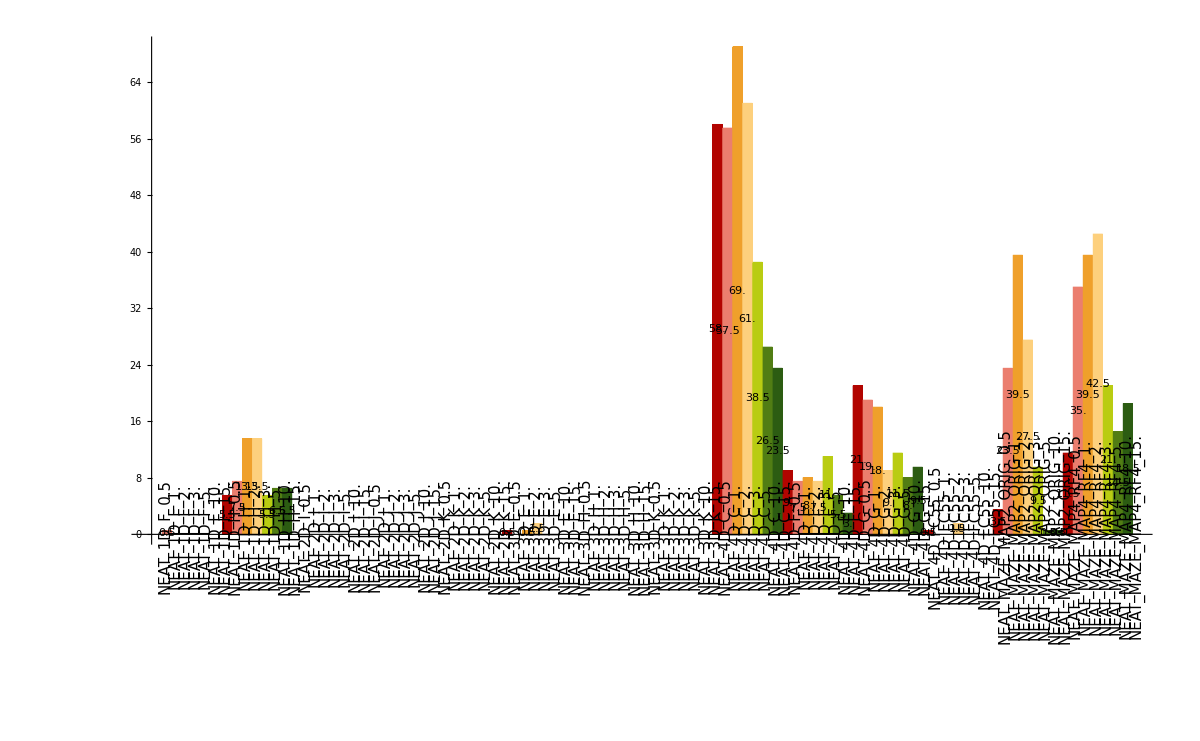

```mathematica
plotBooleanAsBarChart[sortedData,"SUCCESS",7]
```

```mathematica
printBooleanRanksAsTable[sortedData,"SUCCESS",21]//N
```

ID | GPEFS.SPECIES_REPRODUCTION_RATIO | GPEFS.SPECIES_SIZE_MEAN | RANK
1. | 0.05 | 5. | 7.17143
4. | 0.1 | 5. | 8.36429
19. | 1. | 5. | 8.58571
7. | 0.2 | 5. | 9.13571
20. | 1. | 10. | 9.25714
2. | 0.05 | 10. | 9.47857
21. | 1. | 20. | 9.5
5. | 0.1 | 10. | 10.3857
8. | 0.2 | 10. | 10.4857
9. | 0.2 | 20. | 10.8714
3. | 0.05 | 20. | 10.9071
6. | 0.1 | 20. | 11.2929
16. | 0.8 | 5. | 11.3857
18. | 0.8 | 20. | 12.1857
17. | 0.8 | 10. | 12.25
15. | 0.6 | 20. | 12.2643
10. | 0.4 | 5. | 12.4
12. | 0.4 | 20. | 12.6929
14. | 0.6 | 10. | 13.7286
11. | 0.4 | 10. | 14.1286
13. | 0.6 | 5. | 14.5286

## Experiments IV

```mathematica
(*names={"HGP_RANDOMPAR","HGP_BASICPAR","HGP_RESTO2PAR","HGP_TREEPPAR","HGP_TREEP2PAR"};*)
(*names={"HNEAT_BASIC","HNEAT_NOMULT","HNEAT_ALL","HGP","HGP_RANDOM","HGP_BASIC","HGP_RESTO2","HGP_TREEP","HGP_TREEP2"};*)
names={"HNEAT_DELTAS"};
(*names={"HGP_TREEP2PAR"};*)
data=readAllFiles[names,Null,ReplaceParamValues->{"FC55"->"ZFC55"}];
data=assignLabelsByParameters[data,{"SOLVER","ID","RECO.GENERATOR","GPAT.DISTANCE","GP.DISTANCE","GPEFS.SPECIES_REPRODUCTION_RATIO","GPEFS.SPECIES_SIZE_MEAN","NEAT.distanceDelta"},{"ZFC55"->"FC55","hyper.experiments.reco.problem.PatternGeneratorXOR"->"",RegularExpression["hyper.experiments.reco.problem.PatternGenerator"]->""}];
changingParameters[data]
```

{GPAT.DISTANCE_PHENO_HIGH,GPAT.DISTANCE_PHENO_LOW,GPAT.DISTANCE_PHENO_STEPS,ID,NEAT.distanceDelta,NET_ACTIVATIONS,PROBLEM,RECO.GENERATOR,RECO.LINE_SIZE}

```mathematica
saveData[sortedData,"HGP_TREEP2"]
```

```mathematica
(*sdata=selectData[data,{"SOLVER"->"GPAT","GPAT.DISTANCE"->{"SIMPLE_REC5","SIMPLE_REC6","SIMPLE_REC7"}}];*)
(*sdata=removeData[data,{"GPAT.DISTANCE_WEIGHTED_C1"->{0.5,2.}}];*)
(*sdata=removeData[data,{"GPAT.DISTANCE"->{"SIMPLE_REC","SIMPLE_REC2","SIMPLE_REC3"}}];*)
sdata=selectData[data,{"GPEFS.SPECIES_REPRODUCTION_RATIO"->{0.4},"GPEFS.SPECIES_SIZE_MEAN"->{5.}}];
sortedData = sortDataByParams[data,{"ID","RECO.GENERATOR","SOLVER","GPAT.DISTANCE"}];
printAsTable[sortedData,{"SOLVER","GPAT.FUNCTION_IMPL","ID","RECO.GENERATOR","MAZE.MAP","GPAT.DISTANCE","GP.TARGET_FITNESS","GP.DISTANCE","GPEFS.SPECIES_REPRODUCTION_RATIO","GPEFS.SPECIES_SIZE_MEAN","PROBLEM","GPAT.DISTANCE_WEIGHTED_C1"}]
```

ID | PARAM FILE | SOLVER | GPAT.FUNCTION_IMPL | ID | RECO.GENERATOR | MAZE.MAP | GPAT.DISTANCE | GP.TARGET_FITNESS | GP.DISTANCE | GPEFS.SPECIES_REPRODUCTION_RATIO | GPEFS.SPECIES_SIZE_MEAN | PROBLEM | GPAT.DISTANCE_WEIGHTED_C1
NEAT_FC_0.5 | HNEAT_DELTAS/parameters_001.txt | NEAT | NONE | FC | NONE | NONE | NONE | NONE | NONE | NONE | NONE | FIND_CLUSTER | NONE
NEAT_FC_1. | HNEAT_DELTAS/parameters_002.txt | NEAT | NONE | FC | NONE | NONE | NONE | NONE | NONE | NONE | NONE | FIND_CLUSTER | NONE
NEAT_FC_2. | HNEAT_DELTAS/parameters_003.txt | NEAT | NONE | FC | NONE | NONE | NONE | NONE | NONE | NONE | NONE | FIND_CLUSTER | NONE
NEAT_FC_3. | HNEAT_DELTAS/parameters_016.txt | NEAT | NONE | FC | NONE | NONE | NONE | NONE | NONE | NONE | NONE | FIND_CLUSTER | NONE
NEAT_FC_5. | HNEAT_DELTAS/parameters_021.txt | NEAT | NONE | FC | NONE | NONE | NONE | NONE | NONE | NONE | NONE | FIND_CLUSTER | NONE
NEAT_FC_10. | HNEAT_DELTAS/parameters_022.txt | NEAT | NONE | FC | NONE | NONE | NONE | NONE | NONE | NONE | NONE | FIND_CLUSTER | NONE
NEAT_FC_15. | HNEAT_DELTAS/parameters_023.txt | NEAT | NONE | FC | NONE | NONE | NONE | NONE | NONE | NONE | NONE | FIND_CLUSTER | NONE
NEAT_RECO1D_CopyMirrored1D_0.5 | HNEAT_DELTAS/parameters_004.txt | NEAT | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyMirrored1D | NONE | NONE | NONE | NONE | NONE | NONE | RECO | NONE
NEAT_RECO1D_CopyMirrored1D_1. | HNEAT_DELTAS/parameters_007.txt | NEAT | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyMirrored1D | NONE | NONE | NONE | NONE | NONE | NONE | RECO | NONE
NEAT_RECO1D_CopyMirrored1D_2. | HNEAT_DELTAS/parameters_010.txt | NEAT | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyMirrored1D | NONE | NONE | NONE | NONE | NONE | NONE | RECO | NONE
NEAT_RECO1D_CopyMirrored1D_3. | HNEAT_DELTAS/parameters_017.txt | NEAT | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyMirrored1D | NONE | NONE | NONE | NONE | NONE | NONE | RECO | NONE
NEAT_RECO1D_CopyMirrored1D_5. | HNEAT_DELTAS/parameters_024.txt | NEAT | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyMirrored1D | NONE | NONE | NONE | NONE | NONE | NONE | RECO | NONE
NEAT_RECO1D_CopyMirrored1D_10. | HNEAT_DELTAS/parameters_027.txt | NEAT | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyMirrored1D | NONE | NONE | NONE | NONE | NONE | NONE | RECO | NONE
NEAT_RECO1D_CopyMirrored1D_15. | HNEAT_DELTAS/parameters_030.txt | NEAT | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyMirrored1D | NONE | NONE | NONE | NONE | NONE | NONE | RECO | NONE
NEAT_RECO1D_CopyRotated1D_0.5 | HNEAT_DELTAS/parameters_006.txt | NEAT | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyRotated1D | NONE | NONE | NONE | NONE | NONE | NONE | RECO | NONE
NEAT_RECO1D_CopyRotated1D_1. | HNEAT_DELTAS/parameters_009.txt | NEAT | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyRotated1D | NONE | NONE | NONE | NONE | NONE | NONE | RECO | NONE
NEAT_RECO1D_CopyRotated1D_2. | HNEAT_DELTAS/parameters_012.txt | NEAT | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyRotated1D | NONE | NONE | NONE | NONE | NONE | NONE | RECO | NONE
NEAT_RECO1D_CopyRotated1D_3. | HNEAT_DELTAS/parameters_019.txt | NEAT | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyRotated1D | NONE | NONE | NONE | NONE | NONE | NONE | RECO | NONE
NEAT_RECO1D_CopyRotated1D_5. | HNEAT_DELTAS/parameters_026.txt | NEAT | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyRotated1D | NONE | NONE | NONE | NONE | NONE | NONE | RECO | NONE
NEAT_RECO1D_CopyRotated1D_10. | HNEAT_DELTAS/parameters_029.txt | NEAT | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyRotated1D | NONE | NONE | NONE | NONE | NONE | NONE | RECO | NONE
NEAT_RECO1D_CopyRotated1D_15. | HNEAT_DELTAS/parameters_032.txt | NEAT | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyRotated1D | NONE | NONE | NONE | NONE | NONE | NONE | RECO | NONE
NEAT_RECO1D_CopyShifted1D_0.5 | HNEAT_DELTAS/parameters_005.txt | NEAT | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyShifted1D | NONE | NONE | NONE | NONE | NONE | NONE | RECO | NONE
NEAT_RECO1D_CopyShifted1D_1. | HNEAT_DELTAS/parameters_008.txt | NEAT | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyShifted1D | NONE | NONE | NONE | NONE | NONE | NONE | RECO | NONE
NEAT_RECO1D_CopyShifted1D_2. | HNEAT_DELTAS/parameters_011.txt | NEAT | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyShifted1D | NONE | NONE | NONE | NONE | NONE | NONE | RECO | NONE
NEAT_RECO1D_CopyShifted1D_3. | HNEAT_DELTAS/parameters_018.txt | NEAT | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyShifted1D | NONE | NONE | NONE | NONE | NONE | NONE | RECO | NONE
NEAT_RECO1D_CopyShifted1D_5. | HNEAT_DELTAS/parameters_025.txt | NEAT | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyShifted1D | NONE | NONE | NONE | NONE | NONE | NONE | RECO | NONE
NEAT_RECO1D_CopyShifted1D_10. | HNEAT_DELTAS/parameters_028.txt | NEAT | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyShifted1D | NONE | NONE | NONE | NONE | NONE | NONE | RECO | NONE
NEAT_RECO1D_CopyShifted1D_15. | HNEAT_DELTAS/parameters_031.txt | NEAT | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyShifted1D | NONE | NONE | NONE | NONE | NONE | NONE | RECO | NONE
NEAT_XOR_0.5 | HNEAT_DELTAS/parameters_013.txt | NEAT | NONE | XOR | hyper.experiments.reco.problem.PatternGeneratorXOR | NONE | NONE | NONE | NONE | NONE | NONE | XOR | NONE
NEAT_XOR_1. | HNEAT_DELTAS/parameters_014.txt | NEAT | NONE | XOR | hyper.experiments.reco.problem.PatternGeneratorXOR | NONE | NONE | NONE | NONE | NONE | NONE | XOR | NONE
NEAT_XOR_2. | HNEAT_DELTAS/parameters_015.txt | NEAT | NONE | XOR | hyper.experiments.reco.problem.PatternGeneratorXOR | NONE | NONE | NONE | NONE | NONE | NONE | XOR | NONE
NEAT_XOR_3. | HNEAT_DELTAS/parameters_020.txt | NEAT | NONE | XOR | hyper.experiments.reco.problem.PatternGeneratorXOR | NONE | NONE | NONE | NONE | NONE | NONE | XOR | NONE
NEAT_XOR_5. | HNEAT_DELTAS/parameters_033.txt | NEAT | NONE | XOR | hyper.experiments.reco.problem.PatternGeneratorXOR | NONE | NONE | NONE | NONE | NONE | NONE | XOR | NONE
NEAT_XOR_10. | HNEAT_DELTAS/parameters_034.txt | NEAT | NONE | XOR | hyper.experiments.reco.problem.PatternGeneratorXOR | NONE | NONE | NONE | NONE | NONE | NONE | XOR | NONE
NEAT_XOR_15. | HNEAT_DELTAS/parameters_035.txt | NEAT | NONE | XOR | hyper.experiments.reco.problem.PatternGeneratorXOR | NONE | NONE | NONE | NONE | NONE | NONE | XOR | NONE

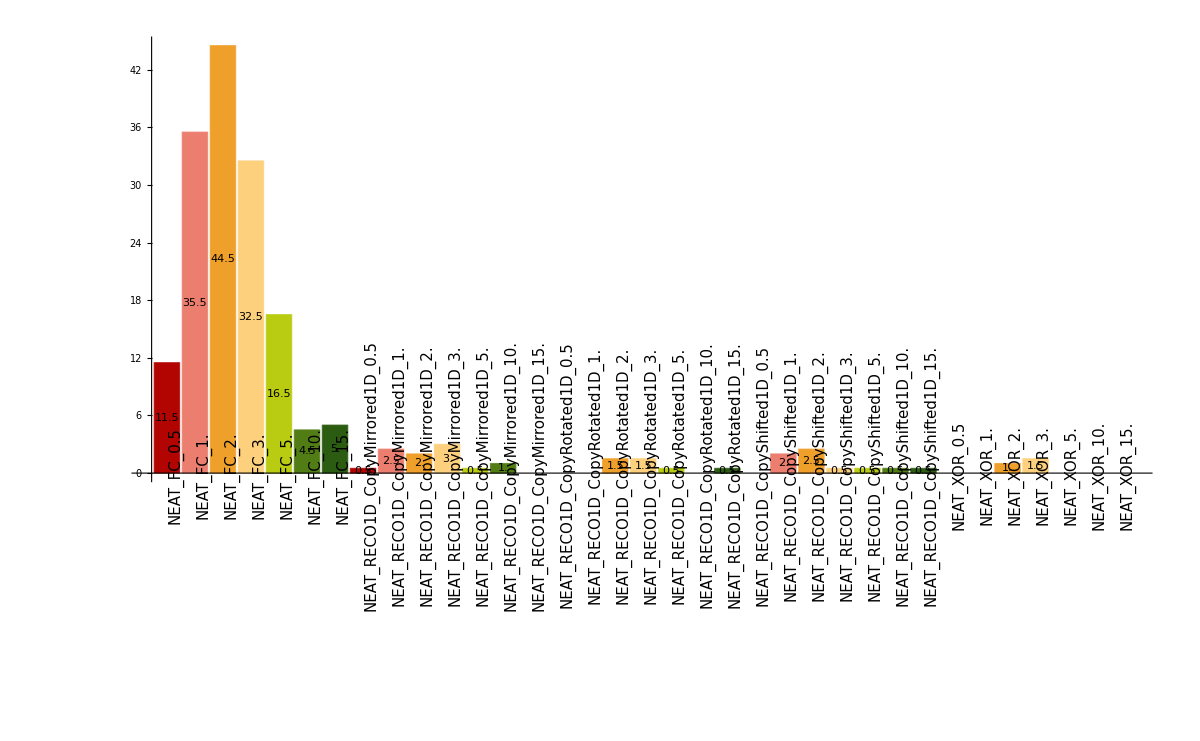

```mathematica
plotBooleanAsBarChart[sortedData,"SUCCESS",7]
```

```mathematica
testFisherExact[{{65,135},{89,111}}]
```

0.017975

```mathematica
plotAsBoxWhiskerChart[sortedData,"BSFG",10]
```

```mathematica
printBooleanRanksAsTable[sortedData,"SUCCESS",21]//N
```

ID | GPEFS.SPECIES_REPRODUCTION_RATIO | GPEFS.SPECIES_SIZE_MEAN | RANK
21. | 1. | 20. | 3.72
19. | 1. | 5. | 4.52
20. | 1. | 10. | 4.82
18. | 0.8 | 20. | 6.82
9. | 0.2 | 20. | 8.46
17. | 0.8 | 10. | 8.6
16. | 0.8 | 5. | 8.88
15. | 0.6 | 20. | 9.78
6. | 0.1 | 20. | 10.26
12. | 0.4 | 20. | 11.18
14. | 0.6 | 10. | 11.66
13. | 0.6 | 5. | 12.14
3. | 0.05 | 20. | 12.46
8. | 0.2 | 10. | 13.68
1. | 0.05 | 5. | 14.02
4. | 0.1 | 5. | 14.32
11. | 0.4 | 10. | 14.48
5. | 0.1 | 10. | 14.52
2. | 0.05 | 10. | 14.9
7. | 0.2 | 5. | 15.62
10. | 0.4 | 5. | 16.16

```mathematica
RANDOM
```

ID | GPEFS.SPECIES_REPRODUCTION_RATIO | GPEFS.SPECIES_SIZE_MEAN | RANK
4. | 0.1 | 5. | 6.7
1. | 0.05 | 5. | 7.2
21. | 1. | 20. | 7.6
19. | 1. | 5. | 8.6
20. | 1. | 10. | 9.2
8. | 0.2 | 10. | 9.4
5. | 0.1 | 10. | 9.5
7. | 0.2 | 5. | 9.7
9. | 0.2 | 20. | 10.5
6. | 0.1 | 20. | 10.5
2. | 0.05 | 10. | 10.5
17. | 0.8 | 10. | 11.7
14. | 0.6 | 10. | 11.8
16. | 0.8 | 5. | 12.
18. | 0.8 | 20. | 12.3
3. | 0.05 | 20. | 12.7
12. | 0.4 | 20. | 13.4
13. | 0.6 | 5. | 14.
10. | 0.4 | 5. | 14.1
15. | 0.6 | 20. | 14.4
11. | 0.4 | 10. | 15.2

```mathematica
BASIC
```

ID | GPEFS.SPECIES_REPRODUCTION_RATIO | GPEFS.SPECIES_SIZE_MEAN | RANK
19. | 1. | 5. | 3.
21. | 1. | 20. | 3.6
20. | 1. | 10. | 4.4
9. | 0.2 | 20. | 6.3
17. | 0.8 | 10. | 7.
6. | 0.1 | 20. | 7.1
3. | 0.05 | 20. | 8.6
18. | 0.8 | 20. | 8.8
16. | 0.8 | 5. | 9.6
12. | 0.4 | 20. | 12.4
14. | 0.6 | 10. | 12.7
4. | 0.1 | 5. | 13.1
8. | 0.2 | 10. | 13.3
15. | 0.6 | 20. | 13.6
5. | 0.1 | 10. | 13.8
1. | 0.05 | 5. | 13.9
13. | 0.6 | 5. | 14.
2. | 0.05 | 10. | 14.3
7. | 0.2 | 5. | 15.4
11. | 0.4 | 10. | 17.
10. | 0.4 | 5. | 19.1

```mathematica
RESTO2
```

ID | GPEFS.SPECIES_REPRODUCTION_RATIO | GPEFS.SPECIES_SIZE_MEAN | RANK
21. | 1. | 20. | 2.7
20. | 1. | 10. | 2.7
18. | 0.8 | 20. | 4.1
19. | 1. | 5. | 4.6
15. | 0.6 | 20. | 6.6
9. | 0.2 | 20. | 6.6
13. | 0.6 | 5. | 8.8
17. | 0.8 | 10. | 9.
16. | 0.8 | 5. | 9.4
6. | 0.1 | 20. | 9.4
14. | 0.6 | 10. | 11.4
12. | 0.4 | 20. | 12.5
11. | 0.4 | 10. | 13.5
3. | 0.05 | 20. | 14.2
1. | 0.05 | 5. | 15.9
10. | 0.4 | 5. | 16.
8. | 0.2 | 10. | 16.
2. | 0.05 | 10. | 16.2
4. | 0.1 | 5. | 16.3
5. | 0.1 | 10. | 17.1
7. | 0.2 | 5. | 18.

```mathematica
TREEP
```

ID | GPEFS.SPECIES_REPRODUCTION_RATIO | GPEFS.SPECIES_SIZE_MEAN | RANK
21. | 1. | 20. | 1.9
19. | 1. | 5. | 3.3
18. | 0.8 | 20. | 3.7
20. | 1. | 10. | 4.3
16. | 0.8 | 5. | 6.2
9. | 0.2 | 20. | 7.8
17. | 0.8 | 10. | 7.9
15. | 0.6 | 20. | 8.9
6. | 0.1 | 20. | 10.2
12. | 0.4 | 20. | 11.5
14. | 0.6 | 10. | 11.7
13. | 0.6 | 5. | 12.4
3. | 0.05 | 20. | 13.1
11. | 0.4 | 10. | 13.4
8. | 0.2 | 10. | 14.7
10. | 0.4 | 5. | 15.7
4. | 0.1 | 5. | 16.
1. | 0.05 | 5. | 16.3
5. | 0.1 | 10. | 16.5
2. | 0.05 | 10. | 17.
7. | 0.2 | 5. | 18.5

```mathematica
TREEP2
```

ID | GPEFS.SPECIES_REPRODUCTION_RATIO | GPEFS.SPECIES_SIZE_MEAN | RANK
21. | 1. | 20. | 2.8
19. | 1. | 5. | 3.1
20. | 1. | 10. | 3.5
18. | 0.8 | 20. | 5.2
15. | 0.6 | 20. | 5.4
12. | 0.4 | 20. | 6.1
16. | 0.8 | 5. | 7.2
17. | 0.8 | 10. | 7.4
14. | 0.6 | 10. | 10.7
9. | 0.2 | 20. | 11.1
13. | 0.6 | 5. | 11.5
11. | 0.4 | 10. | 13.3
3. | 0.05 | 20. | 13.7
6. | 0.1 | 20. | 14.1
8. | 0.2 | 10. | 15.
5. | 0.1 | 10. | 15.7
10. | 0.4 | 5. | 15.9
7. | 0.2 | 5. | 16.5
2. | 0.05 | 10. | 16.5
1. | 0.05 | 5. | 16.8
4. | 0.1 | 5. | 19.5

## Statistics

```mathematica
testMannWhitney[data,"GPAT_H","GPAT_H2","BSF"]
```

median 1: 0.952853

median 2: 0.949325

mean 1: 0.754262

mean 2: 0.528663

variance 1: 0.135817

variance 2: 0.222969

higher/lower variance ratio: 1.64169

U stat: 22636

P-value: 0.0226329

The null hypothesis that the median difference is 0 is rejected at the 5. percent level based on the Mann-Whitney test.

```mathematica
testKruskalWallis[data,{"GP_H","GPAT_H2"},"BSF"]
```

| GPAT_H | GPAT_H2
Mean | 0.754262 | 0.528663
Variance | 0.952853 | 0.949325
Variance | 0.135817 | 0.222969

LocationEquivalenceTest::ntsymmd: The p-value in 1.14305×10^-13, resulting from a test for symmetry, is below 0.05. The tests in {"KruskalWallis"} require that the data is symmetric about a common median.

| Statistic | P-Value
Kruskal-Wallis | 5.19838 | 0.0224202

```mathematica
testFisherExact[{{90,10},{82,18}}]
```

0.152819

```mathematica
testFisherExact[sortedData,"GPAT_E","GPATGP_E","SUCCESS",TwoSided->True,PValueOnly->False]
```

| GPAT_E | GPATGP_E
true | 0. | 1.
false | 200. | 199.
p-value | 1. |

```mathematica
testFisherExactAll[sortedData,"SUCCESS",0.05,TwoSided->True]
```

| 2 | 3 | 4 | 5 | 6
1 | 0.0900213 | 8.70428×10^-7 | 2.99731×10^-15 | 4.39804×10^-33 | 2.71714×10^-43
2 |  | 0.00174071 | 7.22079×10^-10 | 4.23269×10^-25 | 2.75651×10^-34
3 |  |  | 0.00295964 | 3.33437×10^-13 | 3.18256×10^-20
4 |  |  |  | 0.0000196958 | 4.04422×10^-10
5 |  |  |  |  | 0.0552636

## Expressions

```mathematica
sortConfigurationResults[sortedData,"A","BSF",10]
```

1 | 0.996687
12 | 0.983575
100 | 0.970368
78 | 0.96933
10 | 0.968461
60 | 0.968217
79 | 0.963918
73 | 0.958339
68 | 0.956159
35 | 0.955737

```mathematica
Expand[1.5*x1*x2+2.3*x1+x2*x3*x4-1.1*x3]
```

2.3 x1+1.5 x1 x2-1.1 x3+x2 x3 x4

```mathematica
(res=sortConfigurationResults[sortedData,"GP3D_H2","BSF",10,Output->"Expressions"]/.{x0->Subscript[x, 1],x1->Subscript[x, 2],x2->Subscript[x, 3],x3->Subscript[x, 4]})
```

Gen | Expression | Expanded | f
last | {x_2 (-1.+x_1 (x_3+x_2 x_3))} | {-1. x_2+x_1 x_2 x_3+x_1 x_2^2 x_3} | 1.
last | {x_2 (-1.+x_1 x_3+x_1 x_2 x_3)} | {-1. x_2+x_1 x_2 x_3+x_1 x_2^2 x_3} | 1.
last | {-1. x_2+(x_1 x_2+x_1 x_2^2) x_3} | {-1. x_2+x_1 x_2 x_3+x_1 x_2^2 x_3} | 1.
last | {-1. x_2+x_1 x_2 x_3+x_1 x_2^2 x_3} | {-1. x_2+x_1 x_2 x_3+x_1 x_2^2 x_3} | 1.
last | {-1. x_2+x_2 (x_1+x_1 x_2) x_3} | {-1. x_2+x_1 x_2 x_3+x_1 x_2^2 x_3} | 1.
last | {x_1 x_2^2 x_3+x_2 (-1.+x_1 x_3)} | {-1. x_2+x_1 x_2 x_3+x_1 x_2^2 x_3} | 1.
last | {x_1-1. x_2+x_1 (-1.+x_2 x_3+x_2^2 x_3)} | {0.-1. x_2+x_1 x_2 x_3+x_1 x_2^2 x_3} | 1.
last | {x_2 (-1.+(x_1+x_1 x_2) x_3)} | {-1. x_2+x_1 x_2 x_3+x_1 x_2^2 x_3} | 1.
last | {1.08185×10^-8-1. x_2+(x_1 x_2+x_1 x_2^2) x_3} | {1.08185×10^-8-1. x_2+x_1 x_2 x_3+x_1 x_2^2 x_3} | 1.
last | {-1. x_2+x_1 (4.44373×10^-11+x_2 x_3+x_2^2 x_3)} | {4.44373×10^-11 x_1-1. x_2+x_1 x_2 x_3+x_1 x_2^2 x_3} | 1.

```mathematica
(res=sortConfigurationResults[sortedData,"12","BSF",25,Output->"Expressions"]/.{x0->x})
```

Gen | Expression | Expanded | f
last | {0.09977 x (x+Sin[0.787112 ⅇ^(-x^2)])} | {0.09977 x^2+0.09977 x Sin[0.787112 ⅇ^(-x^2)]} | 0.995529
last | {0.0646032 x (ⅇ^(-x^2)+1.55385 x)-0.0344501 Sin[1.-ⅇ^(-x^2)]} | {0.0646032 ⅇ^(-x^2) x+0.100383 x^2-0.0344501 Sin[1.-ⅇ^(-x^2)]} | 0.995316
last | {0.100061 x (0.0156719+x)} | {0.00156814 x+0.100061 x^2} | 0.995278
last | {ⅇ^(-11.8063-Sin[x]^2)+0.0999739 x (0.021377+x)} | {ⅇ^(-11.8063-Sin[x]^2)+0.00213714 x+0.0999739 x^2} | 0.995253
last | {0.100195 x^2} | {0.100195 x^2} | 0.995163
last | {0.0997882 x^2} | {0.0997882 x^2} | 0.995147
last | {-0.0015477+0.100253 x^2} | {-0.0015477+0.100253 x^2} | 0.995127
last | {0.0995871 x^2} | {0.0995871 x^2} | 0.994844
last | {0.0995752 x^2} | {0.0995752 x^2} | 0.99482
last | {0.100443 x^2} | {0.100443 x^2} | 0.994783
last | {0.0999352 (-0.0328145+x) x} | {-0.00327932 x+0.0999352 x^2} | 0.994597
last | {0.0994062 x^2} | {0.0994062 x^2} | 0.994405
last | {0.100651 x^2} | {0.100651 x^2} | 0.994233
last | {4.35401×10^-11+0.100887 x (ⅇ^(-x^2)+x)} | {4.35401×10^-11+0.100887 ⅇ^(-x^2) x+0.100887 x^2} | 0.993847
last | {0.10084 x^2} | {0.10084 x^2} | 0.993554
last | {0.0993273 x (ⅇ^(-33.9284 (3.47822+x)^2)+x)} | {0.0993273 ⅇ^(-33.9284 (3.47822+x)^2) x+0.0993273 x^2} | 0.993273
last | {0.0990122 x^2} | {0.0990122 x^2} | 0.992907
last | {-0.000371379+0.0990141 x^2} | {-0.000371379+0.0990141 x^2} | 0.992889
last | {Sin[0.129682 x] (x-Sin[0.336709 x]-0.196058 Sin[x])} | {x Sin[0.129682 x]-Sin[0.129682 x] Sin[0.336709 x]-0.196058 Sin[0.129682 x] Sin[x]} | 0.992606
last | {0.101464 (-0.763579+x (0.0208029+x))} | {-0.0774756+0.00211074 x+0.101464 x^2} | 0.992428
last | {0.0988539 x^2} | {0.0988539 x^2} | 0.992097
last | {0.101382 x (ⅇ^(-0.332217 x^2)+x)} | {0.101382 ⅇ^(-0.332217 x^2) x+0.101382 x^2} | 0.99195
last | {(0.815193 x^2 (-0.632121 ⅇ^(-(4.80488+x)^2)+x+ⅇ^(-x^2) (2.03518+x)) ArcTan[x])/(√(1+140.445 x^2))} | {(1.65907 ⅇ^(-x^2) x^2 ArcTan[x])/(√(1+140.445 x^2))-(0.5153 ⅇ^(-(4.80488+x)^2) x^2 ArcTan[x])/(√(1+140.445 x^2))+(0.815193 x^3 ArcTan[x])/(√(1+140.445 x^2))+(0.815193 ⅇ^(-x^2) x^3 ArcTan[x])/(√(1+140.445 x^2))} | 0.991336
last | {0.10128 x^2} | {0.10128 x^2} | 0.991321
last | {0.0989743 x (0.0785205+x)} | {0.00777151 x+0.0989743 x^2} | 0.991136

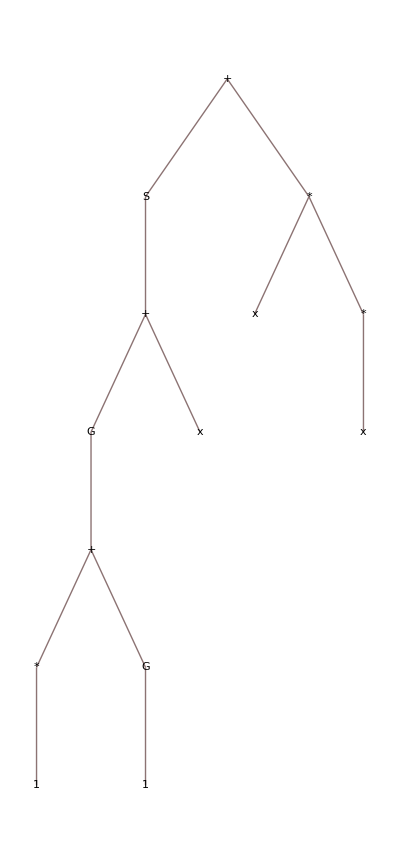
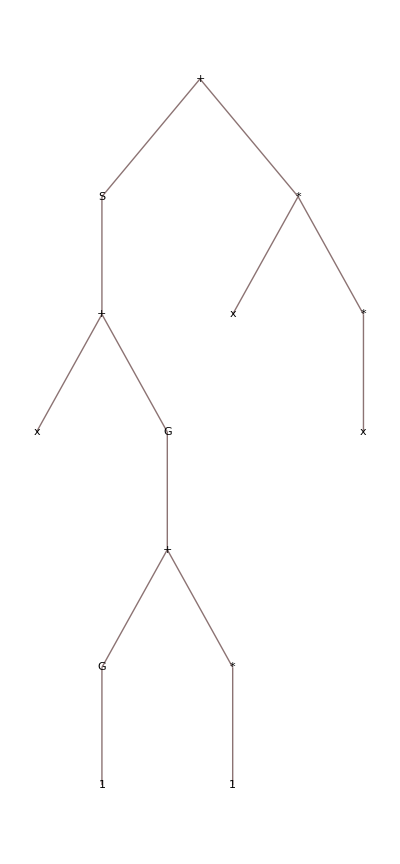
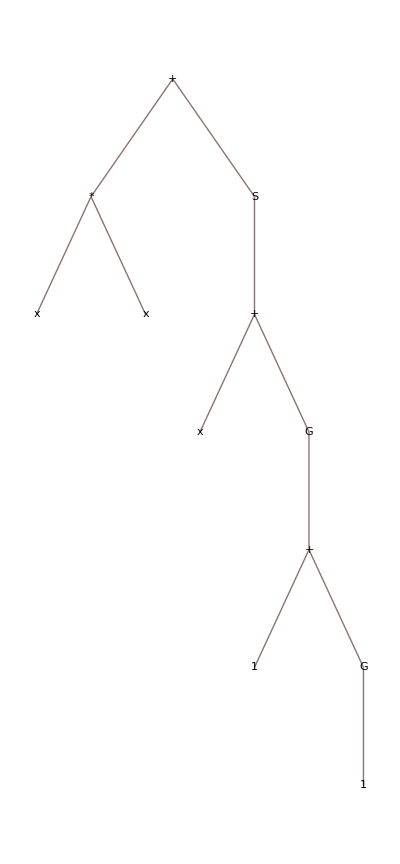
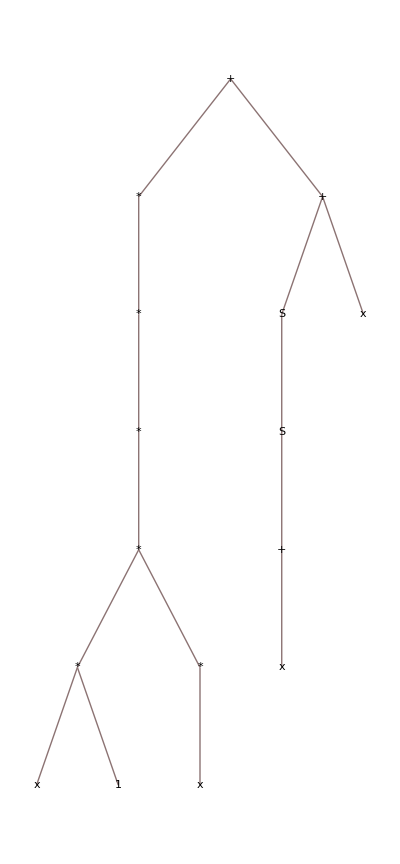
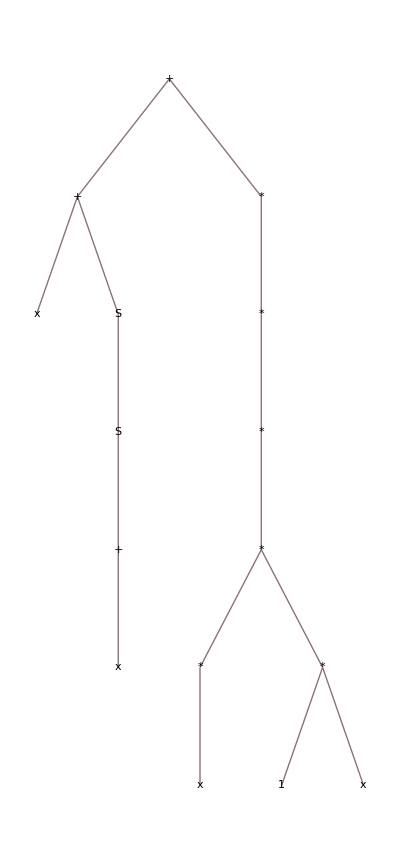
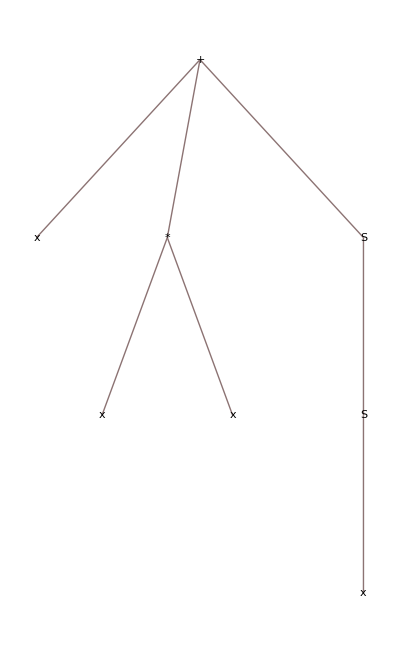
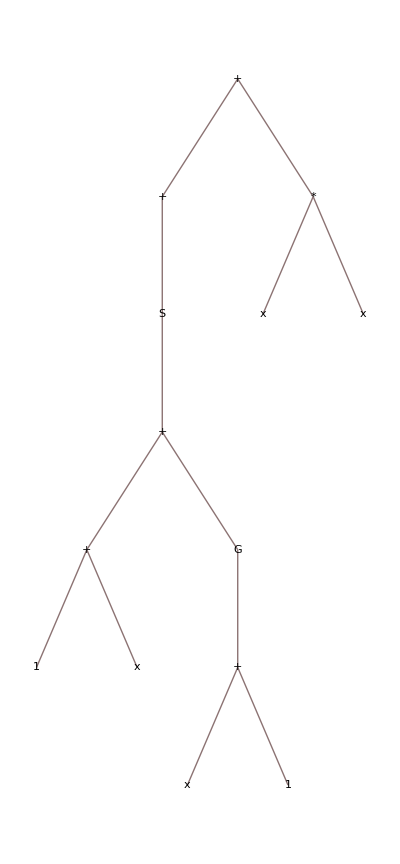
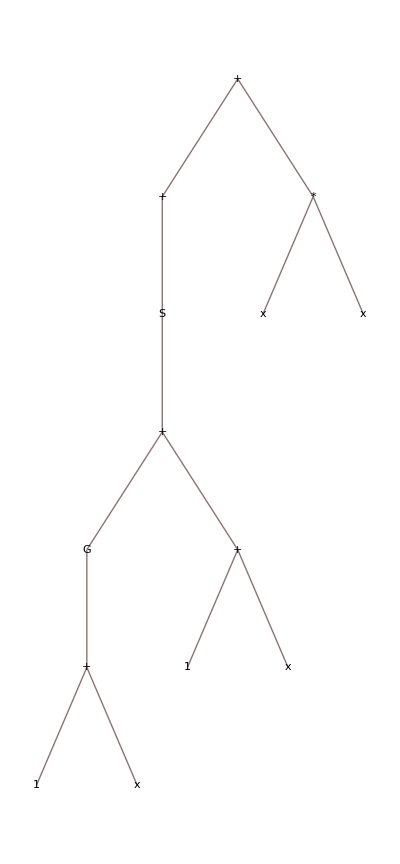
Gen | Genome | Sorted | Simplified | f
last | -Graphics- | -Graphics- | -Graphics- | 0.99656
last | -Graphics- | -Graphics- | -Graphics- | 0.983261
last | -Graphics- | -Graphics- | -Graphics- | 0.978954
last | -Graphics- | -Graphics- | -Graphics- | 0.978529
last | -Graphics- | -Graphics- | -Graphics- | 0.957386
last | -Graphics- | -Graphics- | -Graphics- | 0.956843
last | -Graphics- | -Graphics- | -Graphics- | 0.952837
last | -Graphics- | -Graphics- | -Graphics- | 0.951168
last | -Graphics- | -Graphics- | -Graphics- | 0.940757
last | -Graphics- | -Graphics- | -Graphics- | 0.852304

```mathematica
(res=sortConfigurationResults[sortedData,"A","BSF",10,Output->"BSFGenomes"]/.{x0->x})
```

```mathematica
Export["GP_H2.pdf",%]
```

GP_H2.pdf